# 2-Layer System - Transfer Matrix Method

```mathematica
Clear[t1, tf, ti]
```

## System Setup

```mathematica
tg[a_, b_] =  1/2{{1+a/b(1-(ξ+ⅈ ζ)/a),1-a/b(1+(ξ+ⅈ ζ)/a)},
{1-a/b(1-(ξ+ⅈ ζ)/a),1+a/b(1+(ξ+ⅈ ζ)/a)}};
```

```mathematica
tp[n_,x_]= {{ⅇ^(ⅈ 2 π n x),0},{0,ⅇ^(-ⅈ 2 π n x)}};
```

```mathematica
ti = tg[a, b];
```

```mathematica
tn[x_] = tg[b, b] . tp[b, x];
```

```mathematica
tf[x_] = tg[b, c] . tp[b, x];
```

```mathematica
t1[x_] = tf[x] . ti;
```

## Reflectance

```mathematica
r[x_] =- (t1[x][[2, 1]])/(t1[x][[2, 2]])
```

-(1/4 ⅇ^(2 ⅈ b π x) (1+(a (1-(ⅈ ζ+ξ)/a))/b) (1-(b (1-(ⅈ ζ+ξ)/b))/c)+1/4 ⅇ^(-2 ⅈ b π x) (1-(a (1-(ⅈ ζ+ξ)/a))/b) (1+(b (1+(ⅈ ζ+ξ)/b))/c))/(1/4 ⅇ^(2 ⅈ b π x) (1-(a (1+(ⅈ ζ+ξ)/a))/b) (1-(b (1-(ⅈ ζ+ξ)/b))/c)+1/4 ⅇ^(-2 ⅈ b π x) (1+(a (1+(ⅈ ζ+ξ)/a))/b) (1+(b (1+(ⅈ ζ+ξ)/b))/c))

```mathematica
-((1/4 ⅇ^(2 ⅈ b π x) (1+(a (1-(ⅈ ζ+ξ)/a))/b) (1-(b (1-(ⅈ ζ+ξ)/b))/c)+1/4 ⅇ^(-2 ⅈ b π x) (1)))(a (1-(ⅈ ζ+ξ)/a))/b) (1+(b (1+(ⅈ ζ+ξ)/b))/c))/(1/4 ⅇ^(2 ⅈ b π x) (1-(a (1+(ⅈ ζ+ξ)/a))/b) (1-(b (1-(ⅈ ζ+ξ)/b))/c)+1/4 ⅇ^(-2 ⅈ b π x) (1+(a (1+(ⅈ ζ+ξ)/a))/b) (1+(b (1+(ⅈ ζ+ξ)/b))/c)))
```

```mathematica
R[x_] = Norm[r[x]] //. {a-> 1.46, b-> 1.6,c-> 1.0, ξ-> 0.149, ζ-> 0};
```

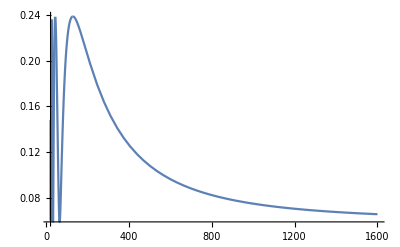

```mathematica
Plot[R[20/x], {x, 20, 1600}]
```

## Transfer Matrix

```mathematica
tf[40/2000].MatrixPower[tn[40/2000], 18].ti/. {a-> 1.46, b-> 1.6,c-> 1.0, ξ-> 0.149, ζ-> 0}
```

{{-0.227362-0.309931 ⅈ,0.849503-0.417756 ⅈ},{-0.380302+0.0820838 ⅈ,-2.28184+2.10505 ⅈ}}

## 3-Layer System

```mathematica
t2[x_] = tf[x] . MatrixPower[tn[x], 19].ti;
```

```mathematica
r2[x_] =- (t2[x][[2, 1]])/(t2[x][[2, 2]]) ;
```

```mathematica
R2[x_] = Norm[r2[x]^2*100] //. {a-> 1.46, b-> 1.6,c-> 1.0, ξ-> 0.149, ζ-> 0};
```

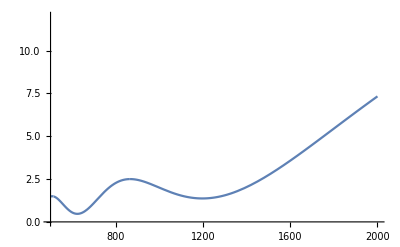

```mathematica
Plot[R2[20/x], {x, 500, 2000}, PlotRange->{0, 12}]
```

```mathematica
SetDirectory["/Volumes/GoogleDrive/Shared drives/ProjectoReflectancia/Notas/Rui/Mathematica"];
```

```mathematica
Points = 1000;
xmax = 2000;
xmin = 500;
data=Table[{(n/Points*(xmax-xmin)+xmin)//N,R2[20/(n/Points*(xmax-xmin)+xmin)]//N},{n,1,Points}];
```

```mathematica
Export["out.dat",data]
```

out.dat